```mathematica
Δ=r^2-2M r+a^2;
Σ=r^2+a^2(Cos[θ])^2;
```

```mathematica
diffep3=metric1-kerr1
```

{{1-(2 M r)/(r^2+a^2 Cos[θ]^2)+((2 M r-r^2-a^2 Cos[θ]^2) (M^3 r ϵ3+(r^2+a^2 Cos[θ]^2)^2))/((r^2+a^2 Cos[θ]^2)^3),-(2 M r)/(r^2+a^2 Cos[θ]^2)-(M r (M^3 r ϵ3+(r^2+a^2 Cos[θ]^2)^2) (-a^2+4 M r-2 (r^2+a^2 Cos[θ]^2)+a^2 Cos[2 θ]))/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)^3),0,(2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)-(2 a M r (M^3 r ϵ3+(r^2+a^2 Cos[θ]^2)^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)},{-(2 M r)/(r^2+a^2 Cos[θ]^2)-(M r (M^3 r ϵ3+(r^2+a^2 Cos[θ]^2)^2) (-a^2+4 M r-2 (r^2+a^2 Cos[θ]^2)+a^2 Cos[2 θ]))/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)^3),-1-(2 M r)/(r^2+a^2 Cos[θ]^2)+(2 M^2 r^2 (M^3 r ϵ3+(r^2+a^2 Cos[θ]^2)^2) (-a^2+4 M r-2 (r^2+a^2 Cos[θ]^2)+a^2 Cos[2 θ]))/((a^2-2 M r+r^2)^2 (r^2+a^2 Cos[θ]^2)^3)+(M^3 r ϵ3 (r^2+a^2 Cos[θ]^2)+(r^2+a^2 Cos[θ]^2)^3)/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)^2+a^2 M^3 r ϵ3 Sin[θ]^2)+(a^2 Sin[θ]^2 (-4 M^5 r^3 ϵ3-4 M^2 r^2 (r^2+a^2 Cos[θ]^2)^2+(a^2+r^2) (r^2+a^2 Cos[θ]^2)^3+a^2 M r (2 M^3 r ϵ3+M^2 ϵ3 (r^2+a^2 Cos[θ]^2)+2 (r^2+a^2 Cos[θ]^2)^2) Sin[θ]^2))/((a^2-2 M r+r^2)^2 (r^2+a^2 Cos[θ]^2)^3),0,a Sin[θ]^2+(2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)-(a Sin[θ]^2 (-4 M^5 r^3 ϵ3-4 M^2 r^2 (r^2+a^2 Cos[θ]^2)^2+(a^2+r^2) (r^2+a^2 Cos[θ]^2)^3+a^2 M r (2 M^3 r ϵ3+M^2 ϵ3 (r^2+a^2 Cos[θ]^2)+2 (r^2+a^2 Cos[θ]^2)^2) Sin[θ]^2))/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)^3)},{0,0,0,0},{(2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)-(2 a M r (M^3 r ϵ3+(r^2+a^2 Cos[θ]^2)^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3),a Sin[θ]^2+(2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)-(a Sin[θ]^2 (-4 M^5 r^3 ϵ3-4 M^2 r^2 (r^2+a^2 Cos[θ]^2)^2+(a^2+r^2) (r^2+a^2 Cos[θ]^2)^3+a^2 M r (2 M^3 r ϵ3+M^2 ϵ3 (r^2+a^2 Cos[θ]^2)+2 (r^2+a^2 Cos[θ]^2)^2) Sin[θ]^2))/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)^3),0,-Sin[θ]^2 (a^2+r^2+(2 a^2 M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2))+Sin[θ]^2 (a^2+r^2+(a^2 M r (2 M^3 r ϵ3+M^2 ϵ3 (r^2+a^2 Cos[θ]^2)+2 (r^2+a^2 Cos[θ]^2)^2) Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3))}}

```mathematica
Collect[diffep3,ϵ3]
```

{{1+(M^3 r ϵ3 (2 M r-r^2-a^2 Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)-(2 M r)/(r^2+a^2 Cos[θ]^2)+(2 M r-r^2-a^2 Cos[θ]^2)/(r^2+a^2 Cos[θ]^2),-(2 M r)/(r^2+a^2 Cos[θ]^2)-(M^4 r^2 ϵ3 (-a^2+4 M r-2 (r^2+a^2 Cos[θ]^2)+a^2 Cos[2 θ]))/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)^3)-(M r (-a^2+4 M r-2 (r^2+a^2 Cos[θ]^2)+a^2 Cos[2 θ]))/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)),0,-(2 a M^4 r^2 ϵ3 Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3)},{-(2 M r)/(r^2+a^2 Cos[θ]^2)-(M^4 r^2 ϵ3 (-a^2+4 M r-2 (r^2+a^2 Cos[θ]^2)+a^2 Cos[2 θ]))/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)^3)-(M r (-a^2+4 M r-2 (r^2+a^2 Cos[θ]^2)+a^2 Cos[2 θ]))/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)),-1-(2 M r)/(r^2+a^2 Cos[θ]^2)+(2 M^2 r^2 (M^3 r ϵ3+(r^2+a^2 Cos[θ]^2)^2) (-a^2+4 M r-2 (r^2+a^2 Cos[θ]^2)+a^2 Cos[2 θ]))/((a^2-2 M r+r^2)^2 (r^2+a^2 Cos[θ]^2)^3)+(M^3 r ϵ3 (r^2+a^2 Cos[θ]^2)+(r^2+a^2 Cos[θ]^2)^3)/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)^2+a^2 M^3 r ϵ3 Sin[θ]^2)+(a^2 Sin[θ]^2 (-4 M^5 r^3 ϵ3-4 M^2 r^2 (r^2+a^2 Cos[θ]^2)^2+(a^2+r^2) (r^2+a^2 Cos[θ]^2)^3+a^2 M r (2 M^3 r ϵ3+M^2 ϵ3 (r^2+a^2 Cos[θ]^2)+2 (r^2+a^2 Cos[θ]^2)^2) Sin[θ]^2))/((a^2-2 M r+r^2)^2 (r^2+a^2 Cos[θ]^2)^3),0,a Sin[θ]^2-(a (a^2+r^2) Sin[θ]^2)/(a^2-2 M r+r^2)+(2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)+(4 a M^2 r^2 Sin[θ]^2)/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2))-(2 a^3 M r Sin[θ]^4)/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2))+ϵ3 ((4 a M^5 r^3 Sin[θ]^2)/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)^3)-(2 a^3 M^4 r^2 Sin[θ]^4)/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)^3)-(a^3 M^3 r Sin[θ]^4)/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)^2))},{0,0,0,0},{-(2 a M^4 r^2 ϵ3 Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)^3),a Sin[θ]^2-(a (a^2+r^2) Sin[θ]^2)/(a^2-2 M r+r^2)+(2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)+(4 a M^2 r^2 Sin[θ]^2)/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2))-(2 a^3 M r Sin[θ]^4)/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2))+ϵ3 ((4 a M^5 r^3 Sin[θ]^2)/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)^3)-(2 a^3 M^4 r^2 Sin[θ]^4)/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)^3)-(a^3 M^3 r Sin[θ]^4)/((a^2-2 M r+r^2) (r^2+a^2 Cos[θ]^2)^2)),0,a^2 Sin[θ]^2+r^2 Sin[θ]^2+(2 a^2 M r Sin[θ]^4)/(r^2+a^2 Cos[θ]^2)-Sin[θ]^2 (a^2+r^2+(2 a^2 M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2))+ϵ3 ((2 a^2 M^4 r^2 Sin[θ]^4)/((r^2+a^2 Cos[θ]^2)^3)+(a^2 M^3 r Sin[θ]^4)/((r^2+a^2 Cos[θ]^2)^2))}}

```mathematica
Limit[kerr1,r->Infinity]
Limit[diffep3,r->Infinity]
```

{{-1,0,0,0},{0,1,0,-a Sin[θ]^2},{0,0,∞,0},{0,-a Sin[θ]^2,0,∞ Sin[θ]^2}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
FullSimplify[diffep3//.{ϵ3->0}]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
rpeq=kerr1[[1,4]]^2-kerr1[[1,1]]*kerr1[[4,4]]
rpeqnum=FullSimplify[rpeq//.{M->1,a->-0.9375}]
sols=Solve[rpeqnum==0,r]
sols//.{θ->Pi/2}
```

(4 a^2 M^2 r^2 Sin[θ]^4)/((r^2+a^2 Cos[θ]^2)^2)-(-1+(2 M r)/(r^2+a^2 Cos[θ]^2)) Sin[θ]^2 (a^2+r^2+(2 a^2 M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2))

1/((r^2+0.878906 Cos[θ]^2)^2)(-1.34799+r) (-0.652015+r) (0.0482798+0.219727 r^2+0.5 r^4+(0.0241399-0.5 r^4) Cos[2 θ]+(-0.0482798-0.219727 r^2) Cos[4 θ]-0.0241399 Cos[6 θ])

{{r→0.652015},{r→1.34799},{r→-0.5 √(-(2. (-5.57067×10^29+5.57067×10^29 Cos[4. θ]))/(-1.26764×10^30+1.26764×10^30 Cos[2. θ])-2. √(((-5.57067×10^29+5.57067×10^29 Cos[4. θ])^2)/((-1.26764×10^30+1.26764×10^30 Cos[2. θ])^2)-(4. (-1.22402×10^29-6.12012×10^28 Cos[2. θ]+1.22402×10^29 Cos[4. θ]+6.12012×10^28 Cos[6. θ]))/(-1.26764×10^30+1.26764×10^30 Cos[2. θ])))},{r→0.5 √(-(2. (-5.57067×10^29+5.57067×10^29 Cos[4. θ]))/(-1.26764×10^30+1.26764×10^30 Cos[2. θ])-2. √(((-5.57067×10^29+5.57067×10^29 Cos[4. θ])^2)/((-1.26764×10^30+1.26764×10^30 Cos[2. θ])^2)-(4. (-1.22402×10^29-6.12012×10^28 Cos[2. θ]+1.22402×10^29 Cos[4. θ]+6.12012×10^28 Cos[6. θ]))/(-1.26764×10^30+1.26764×10^30 Cos[2. θ])))},{r→-0.5 √(-(2. (-5.57067×10^29+5.57067×10^29 Cos[4. θ]))/(-1.26764×10^30+1.26764×10^30 Cos[2. θ])+2. √(((-5.57067×10^29+5.57067×10^29 Cos[4. θ])^2)/((-1.26764×10^30+1.26764×10^30 Cos[2. θ])^2)-(4. (-1.22402×10^29-6.12012×10^28 Cos[2. θ]+1.22402×10^29 Cos[4. θ]+6.12012×10^28 Cos[6. θ]))/(-1.26764×10^30+1.26764×10^30 Cos[2. θ])))},{r→0.5 √(-(2. (-5.57067×10^29+5.57067×10^29 Cos[4. θ]))/(-1.26764×10^30+1.26764×10^30 Cos[2. θ])+2. √(((-5.57067×10^29+5.57067×10^29 Cos[4. θ])^2)/((-1.26764×10^30+1.26764×10^30 Cos[2. θ])^2)-(4. (-1.22402×10^29-6.12012×10^28 Cos[2. θ]+1.22402×10^29 Cos[4. θ]+6.12012×10^28 Cos[6. θ]))/(-1.26764×10^30+1.26764×10^30 Cos[2. θ])))}}

{{r→0.652015},{r→1.34799},{r→0.-0.0000610353 ⅈ},{r→0.+0.0000610353 ⅈ},{r→-0.0000610353},{r→0.0000610353}}

```mathematica
consts={M->1,θ->0.53666691594449,ϵ3->-0.1,a->0.9375,r->1.36724300949377}
MatrixForm[one=kerr1//.consts]
-Det[one]
MatrixForm[two=metric1//.consts]
-Det[two]
MatrixForm[three=diffep3//.consts]
-Det[three]
```

{M→1,θ→0.536667,ϵ3→-0.1,a→0.9375,r→1.36724}

(0.0857545 | 1.08575 | 0 | -0.266079
1.08575 | 2.08575 | 0 | -0.511143
0 | 0 | 2.51851 | 0
-0.266079 | -0.511143 | 0 | 0.783605)

1.65804

(0.083906 | 1.06235 | 0 | -0.260344
1.06235 | 168.223 | 0 | -1.46602
0 | 0 | 2.51851 | 0
-0.260344 | -1.46602 | 0 | 0.780905)

1.58733

(-0.00184848 | -0.023404 | 0 | 0.00573546
-0.023404 | 166.138 | 0 | -0.954879
0 | 0 | 0 | 0
0.00573546 | -0.954879 | 0 | -0.0027001)

0.

```mathematica
(* a>0 ep3>0 killed at equator first *)
(* a<0 ep3>0 killed at equator first *)
(* a<0 ep3<0 killed at pole first *)
(* a>0 ep3<0 killed at pole first *)
```

```mathematica
rpeq=FullSimplify[metric1[[1,4]]^2-metric1[[1,1]]*metric1[[4,4]]];
(*consts={M->1,a->0.9375,ϵ3->-5};*)
consts={M->1,a->0.5,ϵ3->-10^(-4)};
rpeqnum=rpeq//.consts;
rergo=metric1[[1,1]]//.consts;
(*ContourPlot[rpeqnum==0,{r,0,3},{θ,0,Pi},PlotPoints->30]*)
rptot=(rpeqnum//.{r->Sqrt[x^2+z^2],θ->ArcTan[x/z]});
detg=(Sqrt[-Det[metric1//.consts]]//.{r->Sqrt[x^2+z^2],θ->ArcTan[x/z]});
alphasq=(1.0/(-Inverse[metric1//.consts][[1,1]])//.{r->Sqrt[x^2+z^2],θ->ArcTan[x/z]});
gcovrr=(metric1//.consts)[[2,2]]//.{r->Sqrt[x^2+z^2],θ->ArcTan[x/z]};
rergotot=(rergo//.{r->Sqrt[x^2+z^2],θ->ArcTan[x/z]});
rpold=(-r+1+Sqrt[1-a^2])//.consts//.{r->Sqrt[x^2+z^2],θ->ArcTan[x/z]};
```

```mathematica
ContourPlot[{gcovrr},{x,0,2.2},{z,0,2.2},PlotPoints->100]
```

Power::infy: Infinite expression 1/0.` encountered.

∞::indet: Indeterminate expression 0.` ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.` encountered.

General::stop: Further output of Power will be suppressed during this calculation.

∞::indet: Indeterminate expression 0.` ComplexInfinity encountered.

General::stop: Further output of indet will be suppressed during this calculation.

-Graphics-

Power::infy: Infinite expression 1/0.` encountered.

∞::indet: Indeterminate expression 0.` ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.` encountered.

∞::indet: Indeterminate expression 0.` ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.` encountered.

General::stop: Further output of Power will be suppressed during this calculation.

∞::indet: Indeterminate expression 0.` ComplexInfinity encountered.

General::stop: Further output of indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.` encountered.

∞::indet: Indeterminate expression 0.` ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.` encountered.

General::stop: Further output of Power will be suppressed during this calculation.

∞::indet: Indeterminate expression 0.` ComplexInfinity encountered.

General::stop: Further output of indet will be suppressed during this calculation.

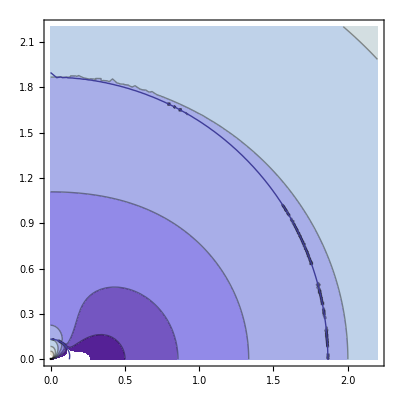

```mathematica
p1=ContourPlot[{alphasq},{x,0,2.2},{z,0,2.2},PlotPoints->30];
p2=ContourPlot[{rptot==0},{x,0,2.2},{z,0,2.2},PlotPoints->30,Contours->{Thick,Red}];
Show[{p1,p2}]
```

```mathematica
Plot3D[(Inverse[metric1][[1,1]]//.consts),{r,1,3},{θ,0,Pi}]
```

-Graphics3D-

```mathematica
Plot3D[(metric1//.consts)[[1,1]],{r,1,3},{θ,0,Pi}]
```

-Graphics3D-

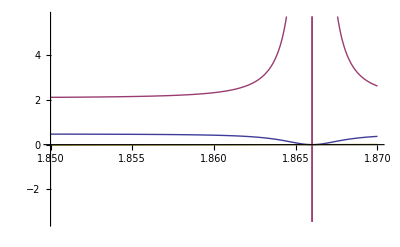

```mathematica
Plot[{alphasq//.{z->0.01},gcovrr//.{z->0.01},rptot//.{z->0.01}},{x,1.85,1.87}]
```

```mathematica
gcovrr//.{z->0.01}//.{x->1.5}
```

2.33336

```mathematica
Solve[(rptot//.{z->0.01})==0,x]
FindRoot[(rptot//.{z->0.01})==0,{x,1.9}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.367085},{x→-0.0430254},{x→-0.0137735-0.0423433 ⅈ},{x→-0.0137735+0.0423433 ⅈ},{x→0.},{x→0.0137735-0.0423433 ⅈ},{x→0.0137735+0.0423433 ⅈ},{x→0.0430254},{x→0.367085}}

{x→1.37161}

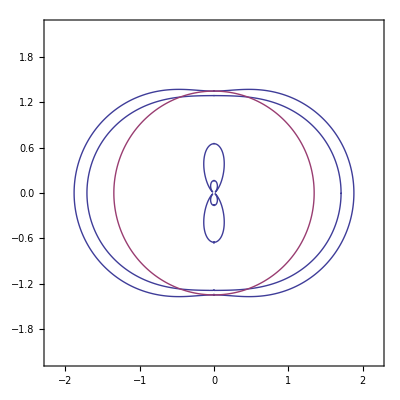

```mathematica
(*ContourPlot[{rptot==0,rergotot==0},{x,-2.2,2.2},{z,-2.2,2.2},PlotPoints->300]*)
ContourPlot[{rptot==0,rpold==0},{x,-2.2,2.2},{z,-2.2,2.2},PlotPoints->300]
(*Plot3D[{detg},{x,-2.2,2.2},{z,-2.2,2.2}]*)
(*Plot3D[{alpha},{x,-2.2,2.2},{z,-2.2,2.2}]*)
```

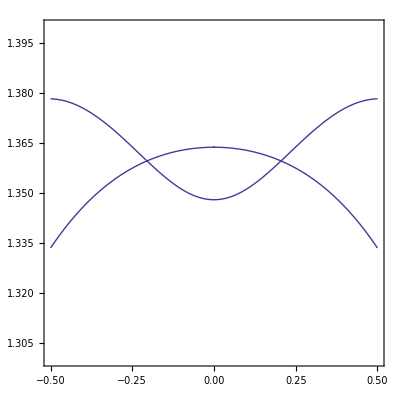

```mathematica
ContourPlot[rptot==0,{x,-0.5,0.5},{z,1.3,1.4},PlotPoints->500]
```

```mathematica
{{0.01399,1.32}}
```

```mathematica
it=metric1//.consts//.{θ->0.001,r->1.32}
gcon=Inverse[it]
alpha=1/Sqrt[-gcon[[1,1]]]
```

{{0.000281527,0.0397565,0,-3.72717×10^-8},{0.0397565,0.0858139,0,0.000126196},{0,0,2.62131,0},{-3.72717×10^-8,0.000126196,0,2.6213×10^-6}}

{{-51.1711,25.5143,0.,-1229.05},{25.5143,-0.180666,0.,9.06049},{0.,0.,0.381489,0.},{-1229.05,9.06049,0.,381036.}}

0.139794

```mathematica
-Det[it]
```

7.10227×10^-10

```mathematica
{{0.00632,1.357}}
```

```mathematica
Solve[rpeqnum==0,r]//.{θ->0}
```

{{r→-0.755621-1.80819 ⅈ},{r→-0.755621+1.80819 ⅈ},{r→0.147489},{r→1.36375},{r→0.652014727323123629867533043818},{r→1.34798527267687637013246695618},{r→-0.9375 ⅈ},{r→0.9375 ⅈ},{r→-0.9375 ⅈ},{r→0.9375 ⅈ}}

```mathematica
(5.5)^(1.0/3.0)
```

1.76517

```mathematica
eqsol1=Limit[rpeq//.{M->1},θ->10^(-5)] (* for ep3<0 *)
eqsol2=Limit[rpeq//.{M->1},θ->Pi/2] (* for ep3>0 *)
(*ContourPlot3D[0==eqsol1,{r,0,3},{ϵ3,-10,10},{a,-1,1}]*)
```

1/((r^2+a^2 Cos[1/100000]^2)^4)(r^4+r ϵ3+2 a^2 r^2 Cos[1/100000]^2+a^4 Cos[1/100000]^4) Sin[1/100000]^2 ((-2+r) r^3 (a^2+r^2)+a^4 (a^2+r^2) Cos[1/100000]^4-a^2 r Cos[1/100000]^2 (-2 (-1+r) r^2+a^2 (1-2 r+Cos[1/50000]))+a^2 r (2 r^2+ϵ3) Sin[1/100000]^2)

((r^3+ϵ3) ((-2+r) r^4+a^2 (r^3+ϵ3)))/r^6

```mathematica
eqsolgen=If[ϵ3<0,eqsol1,eqsol2];
```

```mathematica
ContourPlot3D[0==eqsolgen,{r,0,3},{ϵ3,-10,10},{a,-2,2}]
```

-Graphics3D-

```mathematica
Solve[(eqsol//.{a->0})==0,r]
```

{{r→2},{r→-ϵ3^(1/3)},{r→(-1)^(1/3) ϵ3^(1/3)},{r→-(-1)^(2/3) ϵ3^(1/3)}}

```mathematica
Solve[eqsol==0,r]//.{ϵ3->0.32,a->-0.9}
sols=Solve[eqsol==0,r]
```

{{r→-0.68399},{r→0.341995+0.592353 ⅈ},{r→0.341995-0.592353 ⅈ},{r→-0.500883},{r→1.18474},{r→1.2},{r→0.0580705-0.600517 ⅈ},{r→0.0580705+0.600517 ⅈ}}

{{r→-ϵ3^(1/3)},{r→(-1)^(1/3) ϵ3^(1/3)},{r→-(-1)^(2/3) ϵ3^(1/3)},{r→Root[a^2 ϵ3+a^2 #1^3-2 #1^4+#1^5&,1]},{r→Root[a^2 ϵ3+a^2 #1^3-2 #1^4+#1^5&,2]},{r→Root[a^2 ϵ3+a^2 #1^3-2 #1^4+#1^5&,3]},{r→Root[a^2 ϵ3+a^2 #1^3-2 #1^4+#1^5&,4]},{r→Root[a^2 ϵ3+a^2 #1^3-2 #1^4+#1^5&,5]}}

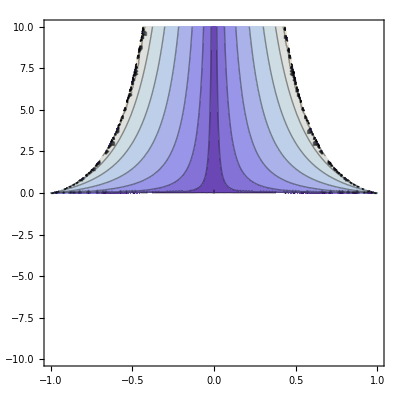

```mathematica
ContourPlot[(r/.sols[[5]]),{a,-1,1},{ϵ3,-10,10}]
```

```mathematica
(r/.sols[[5]])//.{a->-0.9,ϵ3->0.33}
(r/.sols[[6]])//.{a->-0.9,ϵ3->0.33}
```

0.0573172-0.605389 ⅈ

0.0573172+0.605389 ⅈ

```mathematica
rpeqfs=FullSimplify[rpeq];
solsjp1=Solve[rpeqfs==0,r];
```

```mathematica
consts={a->-0.9,ϵ3->0.25,M->1,θ->Pi/2}
solsjp1//.consts
solsjp1[[1]]//.consts
solsjp1[[2]]//.consts
solsjp1[[3]]//.consts
solsjp1[[4]]//.consts
solsjp1[[4]]//.consts
solsjp1[[5]]//.consts
solsjp1[[6]]//.consts
solsjp1[[7]]//.consts
solsjp1[[8]]//.consts
solsjp1[[9]]//.consts
solsjp1[[10]]//.consts
```

{a→-0.9,ϵ3→0.25,M→1,θ→π/2}

{{r→0.31498-0.545562 ⅈ},{r→0.31498+0.545562 ⅈ},{r→-0.629961},{r→-5.55112×10^-17},{r→-0.468676},{r→0.},{r→1.02236},{r→1.31899},{r→0.0636633-0.562457 ⅈ},{r→0.0636633+0.562457 ⅈ}}

{r→0.31498-0.545562 ⅈ}

{r→0.31498+0.545562 ⅈ}

{r→-0.629961}

{r→-5.55112×10^-17}

{r→-5.55112×10^-17}

{r→-0.468676}

{r→0.}

{r→1.02236}

{r→1.31899}

{r→0.0636633-0.562457 ⅈ}

{r→0.0636633+0.562457 ⅈ}

```mathematica
(* Print-out metric for HARM *)
```

```mathematica
For[jj=1,jj≤4,
For[ii=1,ii≤jj,
result=CForm[N[diffep3[[ii,jj]]//.{M->MBH}]]//.{Power->pow,ϵ3->EP3,Cos->cos,Sin->sin,θ->th};
Print["gcovksjp1pert[GIND(",ii-1,",",jj-1,")]=",result,";"];
ii++;
]
jj++;
]
```

gcovksjp1pert[GIND(0,0)]=-4.*EP3*r*(2.*r*(-2.*MBH + r) + pow(a,2) + cos(2.*th)*pow(a,2))*pow(MBH,3)*pow(pow(a,2) + cos(2.*th)*pow(a,2) + 2.*pow(r,2),-3);

gcovksjp1pert[GIND(0,1)]=2.*EP3*pow(MBH,4)*pow(r,2)*pow(pow(r,2) + pow(a,2)*pow(cos(th),2),-3);

gcovksjp1pert[GIND(1,1)]=-1. - 4.*pow(MBH,2)*pow(r,2)*(EP3*r*pow(MBH,3) + pow(r,4) + 2.*pow(a,2)*pow(r,2)*pow(cos(th),2) + pow(a,4)*pow(cos(th),4))*pow(r*(-2.*MBH + r) + pow(a,2),-1)*pow(pow(r,2) + pow(a,2)*pow(cos(th),2),-3) - 2.*MBH*r*pow(pow(r,2) + pow(a,2)*pow(cos(th),2),-1) + (EP3*r*pow(MBH,3)*(pow(r,2) + pow(a,2)*pow(cos(th),2)) + pow(pow(r,2) + pow(a,2)*pow(cos(th),2),3))*pow((r*(-2.*MBH + r) + pow(a,2))*pow(pow(r,2) + pow(a,2)*pow(cos(th),2),2) + EP3*r*pow(a,2)*pow(MBH,3)*pow(sin(th),2),-1) + pow(a,2)*pow(r*(-2.*MBH + r) + pow(a,2),-2)*pow(pow(r,2) + pow(a,2)*pow(cos(th),2),-3)*pow(sin(th),2)*(-4.*EP3*pow(MBH,5)*pow(r,3) - 4.*pow(MBH,2)*pow(r,2)*pow(pow(r,2) + pow(a,2)*pow(cos(th),2),2) + (pow(a,2) + pow(r,2))*pow(pow(r,2) + pow(a,2)*pow(cos(th),2),3) + MBH*r*pow(a,2)*(2.*EP3*r*pow(MBH,3) + EP3*pow(MBH,2)*(pow(r,2) + pow(a,2)*pow(cos(th),2)) + 2.*pow(pow(r,2) + pow(a,2)*pow(cos(th),2),2))*pow(sin(th),2));

gcovksjp1pert[GIND(0,2)]=0.;

gcovksjp1pert[GIND(1,2)]=0.;

gcovksjp1pert[GIND(2,2)]=0.;

gcovksjp1pert[GIND(0,3)]=-2.*a*EP3*pow(MBH,4)*pow(r,2)*pow(pow(r,2) + pow(a,2)*pow(cos(th),2),-3)*pow(sin(th),2);

gcovksjp1pert[GIND(1,3)]=0.125*a*EP3*r*pow(MBH,3)*(-4.*r*(2.*MBH + r)*pow(a,2) + 4.*r*(2.*MBH + r)*cos(2.*th)*pow(a,2) - 1.*pow(a,4) + cos(4.*th)*pow(a,4) + 32.*pow(MBH,2)*pow(r,2))*pow(r*(-2.*MBH + r) + pow(a,2),-1)*pow(pow(r,2) + pow(a,2)*pow(cos(th),2),-3)*pow(sin(th),2);

gcovksjp1pert[GIND(2,3)]=0.;

gcovksjp1pert[GIND(3,3)]=4.*EP3*r*pow(a,2)*(2.*r*(2.*MBH + r) + pow(a,2) + cos(2.*th)*pow(a,2))*pow(MBH,3)*pow(pow(a,2) + cos(2.*th)*pow(a,2) + 2.*pow(r,2),-3)*pow(sin(th),4);

```mathematica
rat11=diffep3[[1,1]]/kerr[[1,1]]
rat14=diffep3[[1,4]]/kerr[[1,4]]
rat44=diffep3[[4,4]]/kerr[[4,4]]
```

-(4 M^3 r ϵ3 (a^2+2 r (-2 M+r)+a^2 Cos[2 θ]))/((-1+(2 M r)/(r^2+a^2 Cos[θ]^2)) (a^2+2 r^2+a^2 Cos[2 θ])^3)

(M^3 r ϵ3)/((r^2+a^2 Cos[θ]^2)^2)

(4 a^2 M^3 r ϵ3 (a^2+2 r (2 M+r)+a^2 Cos[2 θ]) Sin[θ]^2)/((a^2+2 r^2+a^2 Cos[2 θ])^3 (a^2+r^2+(2 a^2 M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)))

```mathematica
FullSimplify[diffep3[[2,2]]//.{ϵ3->0}]
```

0

```mathematica
kerr[[1,4]]//.{M->1,θ->Pi/2}
diffep3[[1,4]]//.{M->1,θ->Pi/2}
```

-(2 a)/r

-(2 a ϵ3)/r^4

```mathematica
prat11=rat11//.{M->1,θ->Pi/2,ϵ3->1}
prat14=rat14//.{M->1,θ->Pi/2,ϵ3->1}
prat44=rat44//.{M->1,θ->Pi/2,ϵ3->1}
```

-(-2+r)/((-1+2/r) r^4)

1/r^3

(a^2 (2+r))/(r^4 (a^2+(2 a^2)/r+r^2))

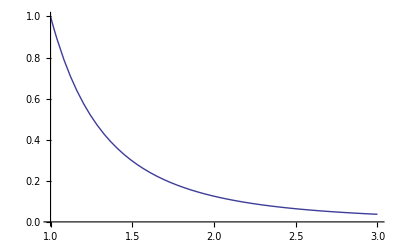

-Graphics-

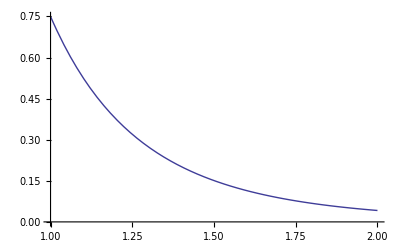

-Graphics-

```mathematica
Plot[prat11,{r,1,3}]
Plot[prat14,{r,1,3}]
Plot[prat44//.{a->1},{r,1,2}]
Plot[prat44//.{a->-1},{r,1,2}]
```

```mathematica
diffep3[[1,2]]
```

(2 M^4 r^2 ϵ3)/((r^2+a^2 Cos[θ]^2)^3)

```mathematica
FullSimplify[Expand[diffep3[[2,2]]],{r>0,M>0,a≥-1,a≤1,θ≥0,θ≤Pi}]
```

$Aborted

```mathematica
diffep3[[2,2]]
```

-1-(2 M r)/(r^2+a^2 Cos[θ]^2)-(4 M^2 r^2 (r^4+M^3 r ϵ3+2 a^2 r^2 Cos[θ]^2+a^4 Cos[θ]^4))/((a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2)^3)+(M^3 r ϵ3 (r^2+a^2 Cos[θ]^2)+(r^2+a^2 Cos[θ]^2)^3)/((a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2)^2+a^2 M^3 r ϵ3 Sin[θ]^2)+(a^2 Sin[θ]^2 (-4 M^5 r^3 ϵ3-4 M^2 r^2 (r^2+a^2 Cos[θ]^2)^2+(a^2+r^2) (r^2+a^2 Cos[θ]^2)^3+a^2 M r (2 M^3 r ϵ3+M^2 ϵ3 (r^2+a^2 Cos[θ]^2)+2 (r^2+a^2 Cos[θ]^2)^2) Sin[θ]^2))/((a^2+r (-2 M+r))^2 (r^2+a^2 Cos[θ]^2)^3)

```mathematica
bad22=(M^3 r ϵ3 (r^2+a^2 Cos[θ]^2)+(r^2+a^2 Cos[θ]^2)^3)/((a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2)^2+a^2 M^3 r ϵ3 Sin[θ]^2)
```

(M^3 r ϵ3 (r^2+a^2 Cos[θ]^2)+(r^2+a^2 Cos[θ]^2)^3)/((a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2)^2+a^2 M^3 r ϵ3 Sin[θ]^2)

```mathematica
FullSimplify[1/bad22]
```

((a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2)^2+a^2 M^3 r ϵ3 Sin[θ]^2)/(M^3 r ϵ3 (r^2+a^2 Cos[θ]^2)+(r^2+a^2 Cos[θ]^2)^3)

```mathematica
bad22
```

(M^3 r ϵ3 (r^2+a^2 Cos[θ]^2)+(r^2+a^2 Cos[θ]^2)^3)/((a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2)^2+a^2 M^3 r ϵ3 Sin[θ]^2)

```mathematica
((r^2+a^2 Cos[θ]^2)^3)/((a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2)^2+a^2 M^3 r ϵ3 Sin[θ]^2)
```

((r^2+a^2 Cos[θ]^2)^3)/((a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2)^2+a^2 M^3 r ϵ3 Sin[θ]^2)